```mathematica
rawData = Import["/home/neophile/Documents/School/QEA/Ref frames/flight1.csv"];
rawData = rawData(*[[1;;20]]*);
rawData = Transpose[rawData];
header = Transpose[rawData][[1]][[{2,  20, 21, 22, 23, 24, 25}]] (*Roll, pitch, yaw, I think*)
(*Gyro units are probably 1/16.384 degrees per second*)
(*Accel units are probably 1/2048 g*)
data = Transpose[Transpose[rawData[[{2,  20, 21, 22, 23, 24, 25}]]][[2;;]]];
data[[1]] -= data[[1]][[1]]; (*Subtract the start time*)
data[[1]] /= 1000000; (*Microseconds to seconds*)
times = data[[1]];
accel = Transpose[data[[{5, 6, 7}]]] * (1/2048) * (9.81);
gyro = Transpose[data[[{2,3,4}]]] * (1/16.384) * (2*Pi/360);
```

{ time (us), gyroADC[0], gyroADC[1], gyroADC[2], accSmooth[0], accSmooth[1], accSmooth[2]}

```mathematica
(*a = Evaluate[Map[Eigenvectors @* RollPitchYawMatrix , gyro]] // N; (*a, b, etc. are intermediate vars*)
b = Map[*)

i = {1,0,0};
j = {0,1,0};
k = {0,0,1};

getPose[prevPose_, θi_, θj_, θk_] := RotationMatrix[θk, prevPose . k] . (RotationMatrix[θj, prevPose . j] . (RotationMatrix[θi, prevPose . i] . prevPose));

dir = {{i,j,k}};
For[n=2,n<Length[gyro]+1,n++,dir = Evaluate[Append[dir, getPose[dir[[Length[dir]]], gyro[[n]][[1]], gyro[[n]][[2]], gyro[[n]][[3]]]]]];
```

```mathematica
tdiff = times[[2;;]] - times[[1;;Length[times]-1]];
dv = accel[[2;;]] * tdiff;
For[n=2,n<Length[dv],n++, dv[[n]] = dir[[n]].dv[[n]]]; (*Rotate velocity changes based on which way the quad's pointing then*)
Assert[Length[tdiff] == Length[dv]];
v = Transpose[dv] . UpperTriangularize[ConstantArray[1,{Length[tdiff],Length[tdiff]}]];
```

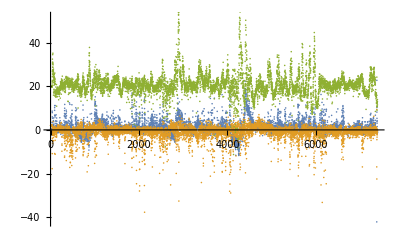

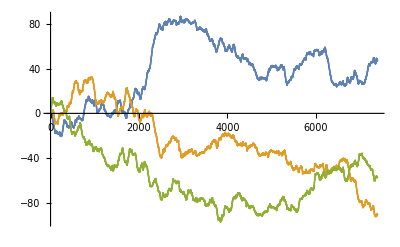

```mathematica
ListPlot[Transpose[accel]]
ListPlot[v]
```